```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2*m],Join[Table[{i,i-1},{i,Range[2,2*m,1]}],Table[{i,i+1},{i,Range[1,2*m,1]}],Table[{2n-1,2*m-2n+2},{n,(m-1)/2+1}],Table[{2*m-2n+2,2n-1},{n,(m-1)/2}]]->t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2*m],Table[{2n,2*m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
TT[t_,m_]:=ReplacePart[0*IdentityMatrix[2*m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,0.+1035.53 ⅈ,0.323223+0. ⅈ,0.-1464.47 ⅈ,-0.176777+0. ⅈ,0.+1035.53 ⅈ,0.0732233+0. ⅈ,0.-1035.53 ⅈ,0.0303301+0. ⅈ,0.+428.932 ⅈ,0.103553+0. ⅈ,0.+428.932 ⅈ,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},299,{{1},12,{1}}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],Tin:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[Tin].J.Tin].B,10000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
Clear[SR,SL]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SR[1,0.001,1,0,7]
```

```mathematica
Clear[SL]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SL[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
tr[1,0.001,1,0,7]
```

tr[1,0.001,1,0,7]

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].TT[t,m].SR[ω,δ,t,ϵ,m].TT[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].TT[t,m].SL[ω,δ,t,ϵ,m].TT[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].TT[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].TT[t,m].grr[ω,δ,t,ϵ,m].TT[t,m]-TT[t,m].GNON[ω,δ,t,ϵ,m].TT[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[1,0.001,1,0,7]
```

2.99999

```mathematica
pris:=pris= Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}]
```

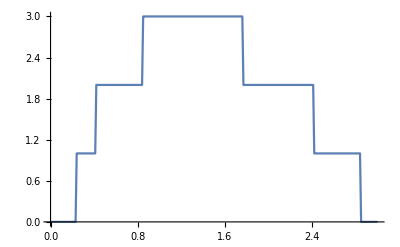

```mathematica
ListLinePlot[pris]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
dist[concentration_,m_]:=dist[concentration,m]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,2m]],concentration]],First],5000]
```

```mathematica
Clear[dist]
```

```mathematica
dist[10,5]//Dimensions
```

{5000,10,2}

```mathematica
F[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,concentration_,dim_,number_]:=Module[{J=β[ω,δ,t,ϵ,dim],abc=dist[concentration,dim][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,concentration}];J]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,concentration_,dim_,number_]:=Module[{Tin=T1[1,dim],T=TT[1,dim]},
sl1=Module[{J1= SL[ω,δ,1,0,dim]},
Do[J1=Inverse[IdentityMatrix[2*dim]-Inverse[Module[{J=β[ω,δ,t,ϵ,dim],abc=dist[concentration,dim][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,concentration}];J]].ConjugateTranspose[T1[1,dim]].J1.T1[1,dim]].Inverse[Module[{J=β[ω,δ,t,ϵ,dim],abc=dist[concentration,dim][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,concentration}];J]],{unitcell,100}];
J1=J1];
Il1:=Inverse[IdentityMatrix[2*dim]-sl1.T.SR[ω,δ,1,0,dim].T].sl1;
Ir1:=Inverse[IdentityMatrix[2*dim]-SR[ω,δ,1,0,dim].T.sl1.T].SR[ω,δ,1,0,dim];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0,dim].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];final=Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]];final]
```

```mathematica
Clear[ca]
```

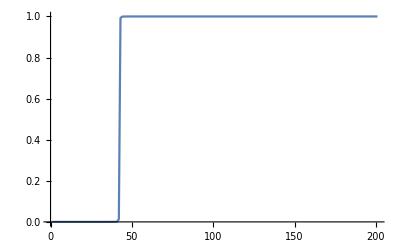

```mathematica
Monitor[Table[CA[ω,0.001,1,0,0,1,3,1],{ω,0,2,0.01}],ω]//ListLinePlot
```

```mathematica
ca[dim_]:=ca[dim]=ParallelTable[CA[1,0.001,1,0,0.5,c,dim,number],{number,3000}]
```

```mathematica
Monitor[Table[ca[dim],{dim,7,27,4}],dim]
```

{{2.08206,2.26669,2.47457,2.6281,1.93699,2.26441,1.91141,2.15299,2.03659,1.32875,2.09332,1.95581,2.4307,1.76287,1.303,2.30948,2969,2.02789,2.44446,1.83589,2.47616,2.47739,2.22531,0.973209,2.17747,2.0918,2.07672,2.06333,2.01247,2.35397,2.39739,2.35031},4,{1}}
 |  |  |  |

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/M101agnr.dat",Table[{x,Abs[Mean[ca[101][[1;;x]]]]/50},{x,10,3000,1}]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/M101agnr.dat

```mathematica
273+472
```

745

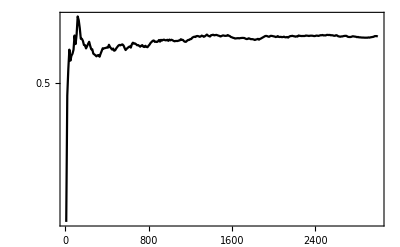

```mathematica
Show[ListLogPlot[Table[{x,Abs[Mean[ca[101][[1;;x]]]]/50},{x,10,3000,10}],Joined->True,Frame->True,PlotStyle->Black],PlotRange->All]
```

```mathematica
Import["~/PhD_new/PhD/fwi/1D/CA_1D/*imp.dat"]
```

{{{-2.,0.00363672},{-1.99,0.0227192},{-1.98,0.0302893},{-1.97,0.0326379},393,{1.97,0.0473926},{1.98,0.0405319},{1.99,0.0311809},{2.,0.00781108}},23,{1}}
 |  |  |  |

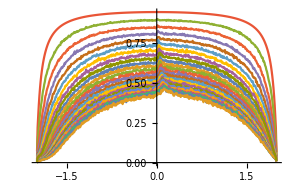

```mathematica
ListLinePlot[%64]
```